{{}}

Piecewise[{{0.357143, 3.8≤x<5.||5.2<x≤6.4}, {0.714286, 5.≤x≤5.2}, {0, True}}]

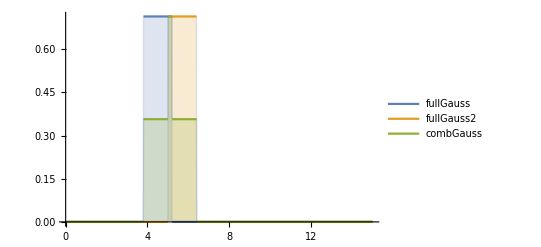

```mathematica
pltRange ={ {} {} }

μ =4.5;
σ = 0.7;

μ2 =5.7;
σ2=0.7;

dist1 = UniformDistribution[{μ-σ, μ+σ}];
dist2 = UniformDistribution[{μ2-σ2, μ2+σ2}];

fullGauss = PDF[dist1,x];
fullGauss2 =  PDF[dist2,x];


combGauss = PDF[MixtureDistribution[{1,1},{dist1,dist2}], x]
Plot[{fullGauss,fullGauss2, combGauss }, {x, 0,15}, PlotRange->Full, Filling->Axis, PlotLegends->"Expressions"]
```